```mathematica
(* KINEMATICS *)
```

```mathematica
me = 0.511;
```

```mathematica
beta[Ep_] := Sqrt[(Ep-me)/(Ep+me)];
gamma[Ep_] := Sqrt[(Ep+me)/2/me];
s[Ep_] := 2*me*(Ep+me);
```

```mathematica
thC[thLAB_,Ep_] := ArcCos[(Cos[thLAB]-beta[Ep])/(1-beta[Ep]*Cos[thLAB])];
EgammaLAB[thLAB_, Ep_, mA_] := me*(1-mA^2/s[Ep])/(1-beta[Ep]*Cos[thLAB]);
```

```mathematica
(* reproduce Fig. 3 of VEPP paper *)
```

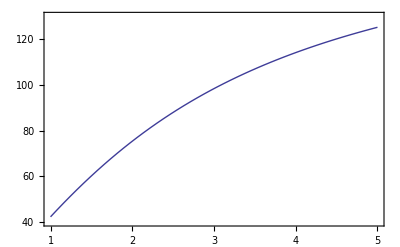

```mathematica
Plot[(180/Pi)*thC[x*Pi/180, 500.],{x,1,5}, PlotRange->{All,{40,130}},Frame->True]
```

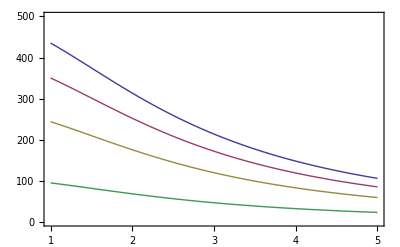

```mathematica
Plot[{EgammaLAB[x*Pi/180, 500., 0.0],EgammaLAB[x*Pi/180, 500., 10.0],EgammaLAB[x*Pi/180, 500., 15.0],EgammaLAB[x*Pi/180, 500., 20.0]}, {x,1,5}, PlotRange->{All,{0,500}}, Frame->True]
```

```mathematica
(* repeat for 5 GeV positrons *)
```

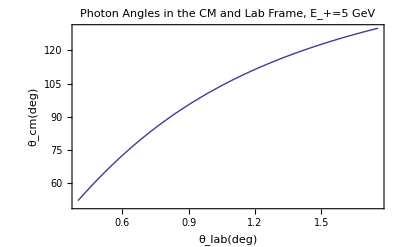

```mathematica
OurAnglePlot = Plot[(180/Pi)*thC[x*Pi/180, 5000.],{x,0.4,2}, PlotRange->{All,{50,130}},Frame->True,PlotLabel->"Photon Angles in the CM and Lab Frame, E_+=5 GeV", FrameLabel->{θ_lab [deg],θ_cm [deg]}]
```

```mathematica
Export["OurAnglePlot.pdf", OurAnglePlot]
```

OurAnglePlot.pdf

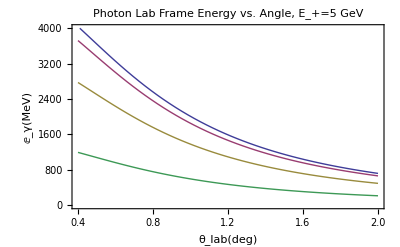

```mathematica
OurEnergyPlot=Plot[{EgammaLAB[x*Pi/180, 5000., 0.0],EgammaLAB[x*Pi/180, 5000., 20.0],EgammaLAB[x*Pi/180, 5000., 40.0],EgammaLAB[x*Pi/180, 5000., 60.0]}, {x,0.4,2.0}, PlotRange->{All,{0,4000}}, Frame->True, PlotLabel->"Photon Lab Frame Energy vs. Angle, E_+=5 GeV", FrameLabel->{θ_lab [deg],E_γ[MeV]}]
```

```mathematica
Export["OurEnergyPlot.pdf", OurEnergyPlot]
```

OurEnergyPlot.pdf

```mathematica
(* SIGNAL/Background (2-gamma) CROSS SECTION *)
```

```mathematica
Clear[r0, gp, eps,m,mA,MA];
```

```mathematica
(* general-purpose trace calculator *)

SpinSum[expr_] := Block[{temp}, 
   temp = Expand[expr];
   temp = temp //. Sp[i_, {x___}, j_]*Sp[j_, {y___}, i_] -> T[i,x,j,y]+M[i]*T[x,j,y]+
   					M[j]*T[i,x,y]+M[i]*M[j]*T[x,y];
   temp = temp //. T[x___, L, i_, R, y___] -> T[x,L,i,y];
   temp = temp //. T[x___, L, i_, L, y___] -> 0;
   temp = temp //. T[x___, R, i_, L, y___] -> T[x,R,i,y];
   temp = temp //. T[x___, R, i_, R, y___] -> 0;

   (* watch out - this only works for 4-point functions *)
   temp = temp //. T[x___, L, y___] -> (1/2)*T[x,y];
   temp = temp //. T[x___, R, y___] -> (1/2)*T[x,y];

   (* trace reductions *)
   temp = temp //. {T[i_] -> 0, T[i_,j_,k_] -> 0, 
                    T[i_,j_,k_,l_,m_] -> 0,
                    T[i_,j_,k_,l_,m_,n_,p_] -> 0};
   temp = temp //. T[i1_,i2_,i3_,i4_,i5_,i6_,i7_,i8_] ->
                   s[i1,i2]*T[i3,i4,i5,i6,i7,i8]-
                   s[i1,i3]*T[i2,i4,i5,i6,i7,i8]+
                   s[i1,i4]*T[i2,i3,i5,i6,i7,i8]-
                   s[i1,i5]*T[i2,i3,i4,i6,i7,i8]+
                   s[i1,i6]*T[i2,i3,i4,i5,i7,i8]-
                   s[i1,i7]*T[i2,i3,i4,i5,i6,i8]+
                   s[i1,i8]*T[i2,i3,i4,i5,i6,i7];
   temp = temp //. T[i1_,i2_,i3_,i4_,i5_,i6_] ->
                   s[i1,i2]*T[i3,i4,i5,i6]-
                   s[i1,i3]*T[i2,i4,i5,i6]+
                   s[i1,i4]*T[i2,i3,i5,i6]-
                   s[i1,i5]*T[i2,i3,i4,i6]+
                   s[i1,i6]*T[i2,i3,i4,i5];
   temp = temp //. T[i1_,i2_,i3_,i4_] ->
                   s[i1,i2]*T[i3,i4]-
                   s[i1,i3]*T[i2,i4]+
                   s[i1,i4]*T[i2,i3];
   temp = temp //. T[i1_,i2_] -> s[i1,i2]*T[1];
   temp = temp //. T[1] -> 4;
                  
   (* clean-up *)
   temp = temp //. s[g[a_],g[a_]] -> 4;
   temp = temp //. s[g[a_],g[b_]] -> g[a,b];
   temp = temp //. s[g[a_],j_] -> k[j,a];
   temp = temp //. s[j_,g[a_]] -> k[j,a];
   temp = Expand[temp];
   (*temp = temp //. g[a_,b_]*g[a_,b_] -> 4;
   temp = temp //. g[a_,b_]*g[b_,a_] -> 4; *)
   temp = temp //. g[a_,b_]*g[b_,c_] -> g[a,c];
   temp = temp //. g[a_,b_]*g[c_,b_] -> g[a,c];
   temp = temp //. g[a_,b_]*g[a_,c_] -> g[b,c];
   temp = temp //. g[a_,b_]*g[c_,a_] -> g[b,c];
   temp = temp //. g[a_,a_] -> 4;
   temp = temp //. g[a_,b_]*g[a_,b_] -> 4;
   temp = temp //. g[a_,b_]*g[b_,a_] -> 4;
   temp = temp //. k[j_,a_]*g[a_,b_] -> k[j,b];
   temp = temp //. k[j_,a_]*g[b_,a_] -> k[j,b];
   temp = temp //. k[i_,a_]*k[i_,a_] -> M[i]^2;
   temp = temp //. k[i_,a_]*k[j_,a_] -> s[i,j];
   temp = temp //. s[i_,i_] -> M[i]^2;
   temp = temp //. s[i_,j_] -> If[i<j, s[i,j], s[j,i]];
   (* convert to Mandelstam variables *)
  (* temp = temp //. {s[1,2] -> (s-M[1]^2-M[2]^2)/2, s[3,4] -> (s-M[3]^2-M[4]^2)/2,
   					s[1,3] -> -(u-M[1]^2-M[3]^2)/2, s[2,4] -> -(u-M[2]^2-M[4]^2)/2,
   					s[1,4] -> -(t-M[1]^2-M[4]^2)/2, s[2,3] -> -(t-M[2]^2-M[3]^2)/2};*)
   temp = temp]
```

```mathematica
(* *************************************************************************** *)
```

```mathematica
(* To test, let's first reproduce QED e+e- -> 2 gamma *)
```

```mathematica
M[1] = m;
M[2] = -m;
M[3] = 0;
M[4] = 0;
```

```mathematica
A = (Sp[2,{g[m],4,g[n]},1]-Sp[2,{g[m],2,g[n]},1]+m*Sp[2,{g[m],g[n]},1])/(u-m^2) + (Sp[2,{g[n],1,g[m]},1]-Sp[2,{g[n],4,g[m]},1]+m*Sp[2,{g[n],g[m]},1])/(t-m^2);
```

```mathematica
Abar = (Sp[1,{g[b],4,g[a]},2]-Sp[1,{g[b],2,g[a]},2]+m*Sp[1,{g[b],g[a]},2])/(u-m^2) + (Sp[1,{g[a],1,g[b]},2]-Sp[1,{g[a],4,g[b]},2]+m*Sp[1,{g[a],g[b]},2])/(t-m^2);
```

```mathematica
Asq = A*Abar*g[m,a]*(g[n,b](*-k[3,n]*k[3,b]/mA^2*));
```

```mathematica
Asq1=Expand[SpinSum[Asq]/4 /. {t->m^2-2*s[1,4], u->m^2-2*s[1,3], s[2,4]->s[1,3], s[1,2]->-m^2+s[1,3]+s[1,4]}]
```

-(2 m^4)/s[1,3]^2+(4 m^2)/s[1,3]-(2 m^4)/s[1,4]^2+(4 m^2)/s[1,4]-(4 m^4)/(s[1,3] s[1,4])+(2 s[1,3])/s[1,4]+(2 s[1,4])/s[1,3]

```mathematica
(* ✓ This is the usual QED expression, e.g. PS eq. (5.105) *)
```

```mathematica
(* Now let's change variables to those of eq. (1) of VEPP paper *)
```

```mathematica
Asq2 = Simplify[Asq1 /. {s[1,3]->m^2*(gp+1)*eps, s[1,4]->m^2*(gp+1)*(1-eps)}]
```

-(2 (1-4 eps^3 (1+gp)^2+2 eps^4 (1+gp)^2-eps (3+4 gp+gp^2)+eps^2 (5+8 gp+3 gp^2)))/((-1+eps)^2 eps^2 (1+gp)^2)

```mathematica
XsecYY = ((4*Pi*r0)^2/64/Pi/(gp-1))*Asq2
```

-((1-4 eps^3 (1+gp)^2+2 eps^4 (1+gp)^2-eps (3+4 gp+gp^2)+eps^2 (5+8 gp+3 gp^2)) π r0^2)/(2 (-1+eps)^2 eps^2 (-1+gp) (1+gp)^2)

```mathematica
(* this looks nothing like Eq. (1) of the VEPP paper! Let's compute the total cross-section *)
```

```mathematica
XsecYYtot = Integrate[Expand[XsecYY], {eps, 1/2*(1-Sqrt[(gp-1)/(gp+1)]), 1/2*(1+Sqrt[(gp-1)/(gp+1)])}, Assumptions->{gp>1}];
```

```mathematica
XsecYYtot =FullSimplify[XsecYYtot, Assumptions->{gp>1}]
```

(π r0^2 (-(3+gp) √(-1+gp^2)-(1+gp (4+gp)) Log[gp-√(-1+gp^2)]))/((-1+gp) (1+gp)^2)

```mathematica
(* ✓ this agrees exactly with Heitler's Eq. (10), p. 270. So, our formula is correct, while the VEPP formula is not. *)
```

```mathematica
(* maybe it's an approximation? Try large gp, small eps *)
```

```mathematica
Map[Simplify, Normal[Series[XsecYY, {gp, Infinity, 3}]]]
```

((-1+eps-3 eps^2+4 eps^3-2 eps^4) π r0^2)/(2 (-1+eps)^2 eps^2 gp^3)-((3-2 eps+2 eps^2) π r0^2)/(2 (-1+eps) eps gp^2)-((1-2 eps+2 eps^2) π r0^2)/(2 (-1+eps) eps gp)

```mathematica
(* this doesn't work... not sure what this VEPP paper formula is meant to be... *)
```

```mathematica
(* *************************************************************************** *)
```

```mathematica
(* now, let's try mA ≠ 0 *)
```

```mathematica
M[1] = m;
M[2] = -m;
M[3] = mA;
M[4] = 0;
```

```mathematica
A = (Sp[2,{g[m],4,g[n]},1]-Sp[2,{g[m],2,g[n]},1]+m*Sp[2,{g[m],g[n]},1])/(u-m^2) + (Sp[2,{g[n],1,g[m]},1]-Sp[2,{g[n],4,g[m]},1]+m*Sp[2,{g[n],g[m]},1])/(t-m^2);
```

```mathematica
Abar = (Sp[1,{g[b],4,g[a]},2]-Sp[1,{g[b],2,g[a]},2]+m*Sp[1,{g[b],g[a]},2])/(u-m^2) + (Sp[1,{g[a],1,g[b]},2]-Sp[1,{g[a],4,g[b]},2]+m*Sp[1,{g[a],g[b]},2])/(t-m^2);
```

```mathematica
Asq = A*Abar*g[m,a]*(g[n,b]-k[3,n]*k[3,b]/mA^2);
```

```mathematica
Asq1=Expand[SpinSum[Asq]/4 //. {t->m^2-2*s[1,4], u->m^2+mA^2-2*s[1,3], s[2,3]->s[1,4]+mA^2/2,s[2,4]->s[1,3]-mA^2/2, s[3,4] -> m^2+s[1,2]-mA^2/2, s[1,2]->-m^2+s[1,3]+s[1,4]}]
```

(2 m^2)/mA^2-(8 m^4)/((mA^2-2 s[1,3])^2)-(6 m^2 mA^2)/((mA^2-2 s[1,3])^2)-(8 m^2)/(mA^2-2 s[1,3])-(4 mA^2)/(mA^2-2 s[1,3])+(2 s[1,3])/mA^2+(2 mA^2 s[1,3])/((mA^2-2 s[1,3])^2)-(4 s[1,3])/(mA^2-2 s[1,3])+(8 m^2 s[1,3])/(mA^2 (mA^2-2 s[1,3]))-(8 s[1,3]^2)/((mA^2-2 s[1,3])^2)+(8 m^2 s[1,3]^2)/(mA^2 (mA^2-2 s[1,3])^2)+(8 s[1,3]^2)/(mA^2 (mA^2-2 s[1,3]))+(8 s[1,3]^3)/(mA^2 (mA^2-2 s[1,3])^2)-(2 m^4)/s[1,4]^2-(m^2 mA^2)/s[1,4]^2+(2 m^2)/s[1,4]-mA^2/s[1,4]+(8 m^4)/((mA^2-2 s[1,3]) s[1,4])+(2 m^2 mA^2)/((mA^2-2 s[1,3]) s[1,4])+(2 s[1,3])/s[1,4]-(4 m^2 s[1,3])/((mA^2-2 s[1,3]) s[1,4])-(4 mA^2 s[1,3])/((mA^2-2 s[1,3]) s[1,4])+(2 s[1,4])/mA^2-(2 mA^2 s[1,4])/((mA^2-2 s[1,3])^2)-(4 s[1,4])/(mA^2-2 s[1,3])+(8 s[1,3] s[1,4])/(mA^2 (mA^2-2 s[1,3]))+(8 s[1,3]^2 s[1,4])/(mA^2 (mA^2-2 s[1,3])^2)

```mathematica
(* let's test it by working out diff. x-section in c-o-m frame, which appeared in the literature, 0903.3941 a.k.a. EST *)
```

```mathematica
Series[Asq1 , {mA,0,0}]
```

(-(2 m^4)/s[1,3]^2+(4 m^2)/s[1,3]-(2 m^4)/s[1,4]^2+(4 m^2)/s[1,4]-(4 m^4)/(s[1,3] s[1,4])+(2 s[1,3])/s[1,4]+(2 s[1,4])/s[1,3])+O[mA]^1

```mathematica
AsqCOM = Simplify[Asq1 /. {m->0, s[1,3]->(1/4)*Ecm^2*(1+mA^2/Ecm^2+cost*(1-mA^2/Ecm^2)),s[1,4]->(1/4)*Ecm^2*(1-cost)*(1-mA^2/Ecm^2)}]
```

-(4 ((1+cost^2) Ecm^4-2 (-1+cost^2) Ecm^2 mA^2+(1+cost^2) mA^4))/((-1+cost^2) (Ecm^2-mA^2)^2)

```mathematica
(* ✓ this agrees exactly with eq. (11) of 0903.3941 *)
```

```mathematica
(* Now let's do it in the electron rest frame, as relevant for our fixed target experiment. Change variables to those of eq. (1) of VEPP paper *)
```

```mathematica
Asq2 = Simplify[Asq1 /. {s[1,3]->m^2*(gp+1)*(1-eps), s[1,4]->m^2*(gp+1)*eps}]
```

-(8 (1+gp)^2 (1-4 eps^3 (1+gp)^2+2 eps^4 (1+gp)^2-eps (3+4 gp+gp^2)+eps^2 (5+8 gp+3 gp^2)) m^6+4 (1+gp) (-1+gp-4 eps^2 (1+gp)^2+4 eps^3 (1+gp)^2+eps (3+4 gp+gp^2)) m^4 mA^2-2 (1+2 gp+eps (1+gp)^2-3 eps^2 (1+gp)^2) m^2 mA^4+(1+eps+eps gp) mA^6)/(eps^2 (1+gp)^2 m^2 (2 (-1+eps) (1+gp) m^2+mA^2)^2)

```mathematica
(* Here's the differential cross section *)
```

```mathematica
XsecAY = FullSimplify[((4*Pi*r0)^2/32/Pi/(gp-1))*Asq2 /. mA->m*MA]
```

-((8 (1+gp)^2 (1+(-1+eps) eps (1+gp) (3+gp+2 (-1+eps) eps (1+gp)))+4 (1+gp) (-1+gp+eps (1+gp) (3+gp+4 (-1+eps) eps (1+gp))) MA^2-2 (1+2 gp-eps (-1+3 eps) (1+gp)^2) MA^4+(1+eps+eps gp) MA^6) π r0^2)/(2 eps^2 (-1+gp) (1+gp)^2 (2 (-1+eps) (1+gp)+MA^2)^2)

```mathematica
XsecAY /. {gp->10000, MA->100, eps->0.4}
```

0.0091839 r0^2

```mathematica
(* expansion when gp >> 1 and MA ~ gp^1/2, as is always the case for us *)
```

```mathematica
Map[Simplify,Normal[Map[Simplify, Normal[Series[Expand[XsecAY /. {MA ->Sqrt[1/x]*y, gp->1/x}], {x,0,1}]] ]/. {x->1/gp, y->mA/m0/Sqrt[gp]}]]
```

-((4+8 eps^2+mA^4/(gp^2 m0^4)+eps (-8+(4 mA^2)/(gp m0^2))) π r0^2)/(2 eps gp (-2+2 eps+mA^2/(gp m0^2)))

```mathematica
% /. {gp->10000, mA->50, m0->0.5, eps->0.4}
```

0.00918916 r0^2

```mathematica
(* make signal cross section plots with mA=50 MeV, for the writeup *)
```

```mathematica
SigE[Eg_,Ep_,mA_] := (XsecAY /. {gp->Ep/me,eps ->Eg/(me+Ep), MA -> mA/me})/(Ep+me);
Jac[th_,Ep_,mA_] := Abs[D[EgammaLAB[xxx,Ep,mA], xxx] /. xxx->th]/(me+Ep);
SigTH[th_,Ep_,mA_] := Jac[th,Ep,mA]*(XsecAY /. {gp->Ep/me,eps ->EgammaLAB[th,Ep,mA]/(me+Ep), MA -> mA/me});
```

```mathematica
EgammaLAB[1.0*Pi/180, 5000, 50.]
```

1025.7

```mathematica
r0 = 0.282;   (* electron radius in sqrt(bn) *)
```

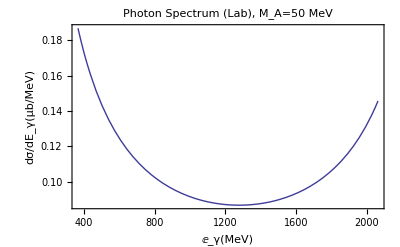

```mathematica
SigEnergyPlot = Plot[SigE[x, 5000., 50]*10^6,{x,EgammaLAB[0.4*Pi/180,5000.,50.],EgammaLAB[2.0*Pi/180,5000.,50.]}, PlotRange->{All,All},Frame->True,PlotLabel->"Photon Spectrum (Lab), M_A=50 MeV", FrameLabel->{E_γ [MeV],(dσ/dE_γ)  [μb/MeV]}]
```

```mathematica
Export["SigEnergyPlot.pdf", SigEnergyPlot]
```

SigEnergyPlot.pdf

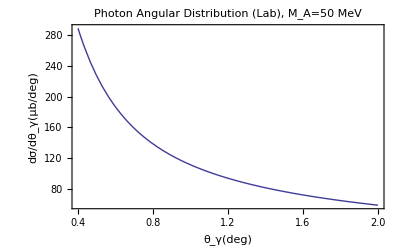

```mathematica
SigAnglePlot = Plot[(Pi/180)*SigTH[x*Pi/180, 5000., 50]*10^6,{x,0.4,2.0}, PlotRange->{All,All},Frame->True,PlotLabel->"Photon Angular Distribution (Lab), M_A=50 MeV", FrameLabel->{θ_γ [deg],(dσ/dθ_γ)  [μb/deg]}]
```

```mathematica
Export["SigAnglePlot.pdf", SigAnglePlot]
```

SigAnglePlot.pdf

```mathematica
(* Now compute the total cross section *)
```

```mathematica
XsecAYtot = Integrate[Expand[XsecAY], {eps, 1/2*(1-MA^2/2/(gp+1))*(1-Sqrt[(gp-1)/(gp+1)]), 1/2*(1-MA^2/2/(gp+1))*(1+Sqrt[(gp-1)/(gp+1)])}, Assumptions->{gp>1}];
```

```mathematica
XsecAYtot =FullSimplify[XsecAYtot, Assumptions->{gp>1}]
```

-(π r0^2 (√((-1+gp)/(1+gp)) (4 (1+gp) (3+gp)+MA^4)-2 (4 gp (4+gp)+(-2+MA^2)^2) ArcTanh[√((-1+gp)/(1+gp))]))/((-1+gp^2) (2+2 gp-MA^2))

```mathematica
((XsecAYtot /. MA->0)/(2*XsecYYtot)) /. gp->3.67585
```

1.

```mathematica
(* ✓ so the QED result is reproduced in the limit MA->0, except for the identical-photon factor of 1/2 in the QED case *)
```

```mathematica
(* ******************************************************************* *)
```

```mathematica
(* numerical evaluation of 2-GAMMA BACKGROUND *)
```

```mathematica
(* first, try to reproduce Fig. 4 of VEPP paper *)
```

```mathematica
r0 = 0.282;   (* electron radius in sqrt(bn) *)
gp = 500./me
```

978.474

```mathematica
XsecYY
```

-1/((-1+eps)^2 eps^2)1.33207×10^-10 (1-961327. eps+2.88006×10^6 eps^2-3.83747×10^6 eps^3+1.91874×10^6 eps^4)

```mathematica
L = 10^8; (* in bn-1 s-1 *)
bin = 5.0;
```

```mathematica
RateYY[Eg_] := L*(bin/ me/(1+gp))*(XsecYY /. eps ->Eg/ me/(1+gp));
```

```mathematica
Egmin=(1/2)*(1-Sqrt[(gp-1)/(gp+1)])*me*(1+gp)
Egmax = (1/2)*(1+Sqrt[(gp-1)/(gp+1)])*me*(1+gp)
```

0.255631

500.255

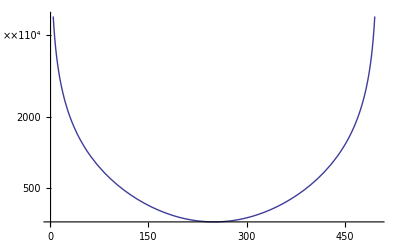

```mathematica
LogPlot[RateYY[Eg], {Eg,Egmin,Egmax}]
```

```mathematica
(* this roughly agrees with Fig. 4 for small Eg, but not large. Our shape makes sense though, due to the 2 gammas being identical! *)
```

```mathematica
(* numerical evaluation of SIGNAL and BACKGROUND (2-gamma only, no smearing) *)
```

```mathematica
Clear[gp, L,r0,MA,mA,th,Ep];
```

```mathematica
Jac[th_,Ep_,mA_] := Abs[D[EgammaLAB[xxx,Ep,mA], xxx] /. xxx->th]/(me+Ep);
Sig[th_,Ep_,mA_] := Jac[th,Ep,mA]*(XsecAY /. {gp->Ep/me,eps ->EgammaLAB[th,Ep,mA]/(me+Ep), MA -> mA/me});
BG[th_,Ep_] := Jac[th,Ep,0]*(XsecYY /. {gp->Ep/me,eps ->EgammaLAB[th,Ep,0.0]/(me+Ep)});
```

```mathematica
DarkPhoton[Ep_, mA_, xmin_, xmax_] := Block[{gp,mAmax,r0,L,sigrate,BGrate},
r0=0.282;
L=10^9;
gp = Ep/me;
mAmax = me*Sqrt[2*(1+gp)];
If[mA>mAmax, Print["ERROR: Maximum A mass for this Ep is", mAmax],{sigrate = L*NIntegrate[Sig[th,Ep,mA],{th,xmin*Pi/180,xmax*Pi/180}]; BGrate = L*NIntegrate[BG[th,Ep],{th,xmin*Pi/180,xmax*Pi/180}]; 
Print["signal rate = ",sigrate," sec-1"];
Print["background rate = ",BGrate," sec-1"];}];
plot1=Plot[{EgammaLAB[x*Pi/180, Ep, 0.0],EgammaLAB[x*Pi/180, Ep, mA]}, {x,xmin,xmax}, PlotRange->{All,All}, Frame->True, FrameLabel->{"θ (degrees)","E_γ (MeV)", "Photon Energy vs. Angle: Blue=γγ, Red=Aγ"}];
plot2=Plot[{(L*Pi/180)*BG[x*Pi/180, Ep],(L*Pi/180)*Sig[x*Pi/180, Ep,mA]}, {x,xmin,xmax}, PlotRange->{All,All}, Frame->True, FrameLabel->{"θ (degrees)","Rate (sec-1 deg-1)", "Rate: Blue=γγ, Red=Aγ"}];
]
```

```mathematica
(* ARGUMENTS of DARKPHOTON[1,2,3,4]: 
1 = positron energy in MeV; 							    2 = dark photon mass in MeV;
3 = minimum angle in degrees;
4 = maximum angle in degrees *)
```

```mathematica
DarkPhoton[5000., 50., 1., 6.]
```

signal rate = 211840. sec-1

background rate = 35964.7 sec-1

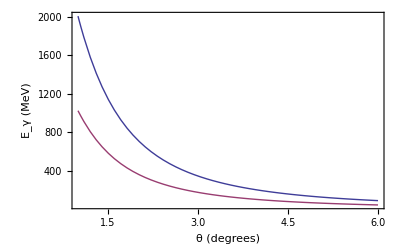

```mathematica
Show[plot1]
```

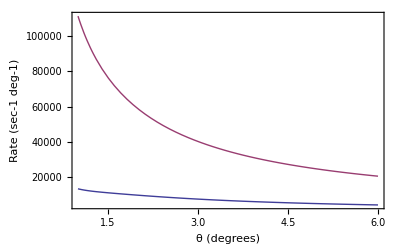

```mathematica
Show[plot2]
```

```mathematica
(* now impose cuts in Egamma(theta) to separate signal and Bg *)
(* here we include fractions energy resolution dE, but NOT the angular measurement uncertainty at this point *)
(* BREM is not included in this exercise *)
```

```mathematica
SmearBG[Eg_,th_,Ep_, dE_] := PDF[NormalDistribution[EgammaLAB[th,Ep,0],EgammaLAB[th,Ep,0]*dE],Eg]*BG[th,Ep];
SmearSig[Eg_,th_,Ep_,mA_,dE_] := PDF[NormalDistribution[EgammaLAB[th,Ep,mA],EgammaLAB[th,Ep,mA]*dE],Eg]*Sig[th,Ep,mA];
```

```mathematica
CutBG[th_,Ep_,dE_,Emax_] := NIntegrate[SmearBG[Eg,th,Ep,dE], {Eg,0,Emax}];
CutSig[th_,Ep_,mA_,dE_,Emax_] := NIntegrate[SmearSig[Eg,th,Ep,mA,dE], {Eg,0,Emax}];
```

```mathematica
(* the cut imposed is Egamma[theta] < Egamma[theta, BG]*Delta *)
(* in the future, can explore Delta[theta]; for now it is a theta-independent constant *)
```

```mathematica
DarkPhotonCUT[Ep_, mA_, xmin_, xmax_, dE_, Delta_] := Block[{Eg,gp,mAmax,r0,L,sigrate,BGrate,dth,Nstep},
r0=0.282;
L=10^9;
Nstep = 1000;
gp = Ep/me;
dth = (xmax-xmin)*Pi/180/Nstep;
mAmax = me*Sqrt[2*(1+gp)];
If[mA>mAmax, Print["ERROR: Maximum A mass for this Ep is", mAmax],{sigrate = L*dth*Sum[CutSig[xmin*Pi/180+i*dth,Ep,mA,dE,EgammaLAB[xmin*Pi/180+i*dth,Ep,0]*Delta], {i,0,Nstep}];
BGrate = L*dth*Sum[CutBG[xmin*Pi/180+i*dth,Ep,dE,EgammaLAB[xmin*Pi/180+i*dth,Ep,0]*Delta],{i,0,Nstep}]; 
Print["signal rate after cut = ",sigrate," sec-1"];
Print["background rate after cut = ",BGrate," sec-1"];}];
]
```

```mathematica
(* ARGUMENTS of DARKPHOTONCUT[1,2,3,4,5,6]: 
1 = positron energy in MeV; 							    2 = dark photon mass in MeV;
3 = minimum angle in degrees;
4 = maximum angle in degrees;
5 = energy resolution (fractional);
6 = energy cut Delta: Egamma[theta] < Egamma[theta, BG]*Delta 
*)
```

```mathematica
DarkPhotonCUT[5000.,50.,1.,6.,0.1,0.8]
```

signal rate after cut = 212170. sec-1

background rate after cut = 819.19 sec-1

```mathematica
(* ****************************************************************** *)
```

```mathematica
(* Now let's add the Bremsstrahlung background. We will not calculate it independently, relying instead on the VEPP paper formula corrected, and implemented, by Jim. The following is taken straight out of Bremsstrahlung.nb *)
```

```mathematica
α=1/137.;

AA[Eplus_]:=4 α r0^2(Eplus/0.511)^2/Pi     (* ✓ *)(* cm^2*)(* the gamma_+== Eplus/0.511 term is missing from VEPP paper *)
B2[x_,y_,Eplus_]:= (4 α (Eplus/0.511) (1-y)/(y(1+x)))^2;  (* ✓ *)
sinθ[x_,Eplus_]:=Sqrt[x]/(Eplus/0.511)  (* for conversion from dΩ to dθ *)    (* ✓ *)
X[θ_,Eplus_]:=(Eplus/0.511)^2 θ^2  (* ✓ *)
Y[energy_,Eplus_]:=energy/Eplus (* ✓ *)

f1[y_,Eplus_]:= 1/(y Eplus);    (* ✓   ie, this is 1/photonEnergy  *)
f2[x_,y_]:=(2y-2)/(1+x)^2;      (* ✓ *)
f3[x_,y_]:=12x(1-y)/(1+x)^4;    (* ✓ *)
f4[x_,y_]:=(2-2y+y^2)/(1+x)^2;    (* ✓ *)
f5[x_,y_]:=4x(1-y)/(1+x)^4;    (* ✓ *)
f6[x_,y_,Eplus_]:=2 Log[2 (Eplus/0.511) (1-y)/y];
f7[x_,y_,Eplus_]:=(1+2/B2[x,y,Eplus])Log[1+B2[x,y,Eplus]];

(* differential cross sections.  Note order of arguments = (Ephoton(y), ThetaPhoton(x), Ebeam) *)
dσdEdO[y_,x_,Eplus_]:= AA [Eplus]f1[y,Eplus](f2[x,y]+f3[x,y] +(f4[x,y]-f5[x,y])(1+f6[x,y,Eplus]-f7[x,y,Eplus]));

dσdEdθ[y_,x_,Eplus_]:=2Pi sinθ[x,Eplus] dσdEdO[y,x,Eplus];
```

```mathematica
(* for simplicity, convert it into "my" notation *)
```

```mathematica
BREM[Eg_,th_,Ep_]:= dσdEdθ[Y[Eg,Ep],X[th, Ep], Ep];
```

```mathematica
SmearBREM[Eg_,th_,Ep_, dE_] := NIntegrate[PDF[NormalDistribution[Egreal,Egreal*dE],Eg]*BREM[Egreal,th,Ep], {Egreal,Eg*(1-3*dE), Eg*(1+3*dE)}];
```

```mathematica
SmearBREM[300.,Pi/180.,5000.,0.02]
```

NIntegrate[PDF[NormalDistribution[Egreal,Egreal 0.02],300.] BREM[Egreal,0.0174533,5000.],{Egreal,300. (1-3 0.02),300. (1+3 0.02)}]

```mathematica
BremEstimate[Eg_, xmin_, xmax_] := NIntegrate[BREM[Eg,th,5000.], {th, xmin*Pi/180., xmax*Pi/180.}]
```

```mathematica
LogPlot[BremEstimate[Eg, 0.5, 1.5], {Eg, 10, 2000}]
```

-Graphics-

```mathematica
(* ****************************************************************** *)
```

```mathematica
(* ***** now try smearing the angle as well ***** *)
(* here BREM is finally included *)
```

```mathematica
SmearAllBG[Eobs_,THobs_,Ep_, dE_, dth_] :=  NIntegrate[PDF[NormalDistribution[EgammaLAB[th,Ep,0],EgammaLAB[th,Ep,0]*dE],Eobs]*PDF[NormalDistribution[th,dth],THobs]*BG[th,Ep], {th,THobs-3*dth,THobs+3*dth}];
```

```mathematica
SmearAllBREM[Eobs_,THobs_,Ep_, dE_, dth_] := Block[{Dth, Nstep, temp}, 
Nstep=10;
Dth = 4*dth/Nstep;
temp = Dth*Sum[PDF[NormalDistribution[THobs-2*dth+i*Dth,dth],THobs]*SmearBREM[Eobs,THobs-2*dth+i*Dth,Ep,dE], {i,0,Nstep}]];
```

```mathematica
SmearAllSig[Eobs_,THobs_,Ep_,mA_, dE_, dth_] := NIntegrate[PDF[NormalDistribution[EgammaLAB[th,Ep,mA],EgammaLAB[th,Ep,mA]*dE],Eobs]*PDF[NormalDistribution[th,dth],THobs]*Sig[th,Ep,mA], {th,THobs-3*dth,THobs+3*dth}];
```

```mathematica
CutAllBG[TH_,Ep_,dE_,Emin_,Emax_,dth_] := Block[{DE, Nstep, temp}, 
Nstep=10;
DE = (Emax-Emin)/Nstep;
temp = DE*Sum[SmearAllBG[Emin+DE*i,TH,Ep,dE, dth],{i,0,Nstep}]];
CutAllSig[TH_,Ep_,mA_,dE_,Emin_,Emax_,dth_] := Block[{DE, Nstep, temp}, 
Nstep=10;
DE = (Emax-Emin)/Nstep;
temp = DE*Sum[SmearAllSig[Emin+DE*i,TH,Ep,mA,dE, dth], {i,0,Nstep}]];
CutAllBREM[TH_,Ep_,dE_,Emin_,Emax_,dth_] := Block[{DE, Nstep, temp}, 
Nstep=10;
DE = (Emax-Emin)/Nstep;
temp = DE*Sum[SmearAllBREM[Emin+DE*i,TH,Ep,dE, dth],{i,0,Nstep}]];
```

```mathematica
DarkPhotonAllCUT[Ep_, mA_, xmin_, xmax_, dE_,Delta_, dx_] := Block[{Eg,gp,mAmax,r0,L,sigrate,BGrate,BREMrate,Dth,Nstep,time,epslimit},
r0=0.282;
L=10^9; (* lumi in bn-1 sec-1 *)
time = 10^7;  (* run time in sec *)
Nstep = 10;
gp = Ep/me;
Dth = (xmax-xmin)*Pi/180/Nstep;
mAmax = me*Sqrt[2*(1+gp)];
If[mA>mAmax, Print["ERROR: Maximum A mass for this Ep is", mAmax],{sigrate = L*Dth*Sum[CutAllSig[xmin*Pi/180+i*Dth,Ep,mA,dE,EgammaLAB[xmin*Pi/180+i*Dth,Ep,mA]*(1-Delta), EgammaLAB[xmin*Pi/180+i*Dth,Ep,mA]*(1+Delta),dx*Pi/180], {i,0,Nstep}];
BGrate = L*Dth*Sum[CutAllBG[xmin*Pi/180+i*Dth,Ep,dE,EgammaLAB[xmin*Pi/180+i*Dth,Ep,mA]*(1-Delta), EgammaLAB[xmin*Pi/180+i*Dth,Ep,mA]*(1+Delta),dx*Pi/180],{i,0,Nstep}]; 
BREMrate = L*Dth*Sum[CutAllBREM[xmin*Pi/180+i*Dth,Ep,dE,EgammaLAB[xmin*Pi/180+i*Dth,Ep,mA]*(1-Delta), EgammaLAB[xmin*Pi/180+i*Dth,Ep,mA]*(1+Delta),dx*Pi/180],{i,0,Nstep}];
Print ["Dark photon mass = ", mA];
Print["signal rate after cut (alpha'=alpha) = ",sigrate," sec-1"];
Print["2-gamma background rate after cut = ",BGrate," sec-1"];
Print["BREM background rate after cut = ",BREMrate," sec-1"];}];
epslimit = 5*Sqrt[(BGrate+BREMrate)*time]/(sigrate*time);
Print["5-sigma discovery reach (stat-only) in eps is ", epslimit];
epslimit=epslimit
]
```

```mathematica
(* ARGUMENTS of DARKPHOTONALLCUT[1,2,3,4,5,6,7]: 
1 = positron energy in MeV; 							   
 2 = dark photon mass in MeV;
3 = minimum angle in degrees;
4 = maximum angle in degrees;
5 = energy resolution (fractional);
6 = energy cut Delta: 
Egamma[THobs, mA]*(1-Delta)< Eobs[THobs] < Egamma[THobs, mA]*(1+Delta);
7 = angle resolution, in degrees  

The function returns the 5-sigma discovery reach in eps=alpha'/alpha 
*)
```

```mathematica
DarkPhotonAllCUT[5000.,50.,0.5,1.5,0.02,0.05, 0.5*10^(-3)/Pi*180]
```

Dark photon mass = 50.

signal rate after cut (alpha'=alpha) = 117619. sec-1

2-gamma background rate after cut = 1.92423×10^-90 sec-1

BREM background rate after cut = 1119.87 sec-1

5-sigma discovery reach (stat-only) in eps is 4.49859×10^-7

4.49859×10^-7

```mathematica
(* now try to make a reach plot *)
```

```mathematica
mAmax = me*Sqrt[2*(5000./me+1)]
```

71.4879

```mathematica
ReachTable=Table[{10.*(1+i),DarkPhotonAllCUT[5000.,10.*(1+i),0.5,1.5,0.02,0.05, 0.5*10^(-3)/Pi*180]},{i,0,6}]
```

Dark photon mass = 10.

signal rate after cut (alpha'=alpha) = 31290.9 sec-1

2-gamma background rate after cut = 13688.4 sec-1

BREM background rate after cut = 800.219 sec-1

5-sigma discovery reach (stat-only) in eps is 6.08227×10^-6

Dark photon mass = 20.

signal rate after cut (alpha'=alpha) = 36494.5 sec-1

2-gamma background rate after cut = 3905.45 sec-1

BREM background rate after cut = 831.111 sec-1

5-sigma discovery reach (stat-only) in eps is 2.98177×10^-6

Dark photon mass = 30.

signal rate after cut (alpha'=alpha) = 47369.2 sec-1

2-gamma background rate after cut = 0.840948 sec-1

BREM background rate after cut = 887.218 sec-1

5-sigma discovery reach (stat-only) in eps is 9.94707×10^-7

Dark photon mass = 40.

signal rate after cut (alpha'=alpha) = 69179.9 sec-1

2-gamma background rate after cut = 9.68865×10^-23 sec-1

BREM background rate after cut = 977.646 sec-1

5-sigma discovery reach (stat-only) in eps is 7.14629×10^-7

Dark photon mass = 50.

signal rate after cut (alpha'=alpha) = 117619. sec-1

2-gamma background rate after cut = 1.92423×10^-90 sec-1

BREM background rate after cut = 1119.87 sec-1

5-sigma discovery reach (stat-only) in eps is 4.49859×10^-7

Dark photon mass = 60.

signal rate after cut (alpha'=alpha) = 263686. sec-1

2-gamma background rate after cut = 5.1148×10^-235 sec-1

BREM background rate after cut = 1351.88 sec-1

5-sigma discovery reach (stat-only) in eps is 2.20472×10^-7

Dark photon mass = 70.

signal rate after cut (alpha'=alpha) = 2.49042×10^6 sec-1

2-gamma background rate after cut = 0. sec-1

BREM background rate after cut = 1880.57 sec-1

5-sigma discovery reach (stat-only) in eps is 2.75323×10^-8

{{10.,6.08227×10^-6},{20.,2.98177×10^-6},{30.,9.94707×10^-7},{40.,7.14629×10^-7},{50.,4.49859×10^-7},{60.,2.20472×10^-7},{70.,2.75323×10^-8}}

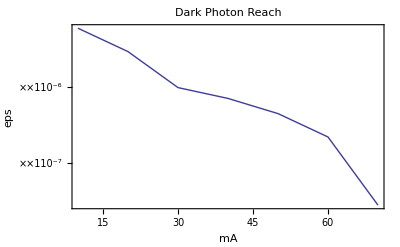

```mathematica
plot1=ListLogPlot[ReachTable, Joined->True, Frame->True, PlotLabel->"Dark Photon Reach", FrameLabel->{mA,eps}]
```

```mathematica
Export["ReachPlot1.pdf", plot1]
```

ReachPlot1.pdf

```mathematica
(* let's test if I reproduce the VEPP paper results; need to switch L->10^8 in DarkPhotonAllCUT function *)
```

```mathematica
DarkPhotonAllCUT[500.,15.,1.5,4.5,0.05,0.15, 0.1]
```

Dark photon mass = 15.

signal rate after cut (alpha'=alpha) = 1.17758×10^6 sec-1

2-gamma background rate after cut = 0.0000191915 sec-1

BREM background rate after cut = 27130.6 sec-1

5-sigma discovery reach (stat-only) in eps is 2.2116×10^-7

2.2116×10^-7

```mathematica
(* Sounds reasonable. They claim improvement of ~10 thanks to positron veto, that would bring this roughly in line with their estimates, see VEPP3 contour in Fig. 9 *)
```

```mathematica
mAmax = me*Sqrt[2*(500./me+1)]
```

22.6169

```mathematica
ReachTableVEPP=Table[{(5.0+i*3.0)*10^(-3),DarkPhotonAllCUT[500.,5.0+i*3.0,1.5,4.5,0.025,0.075, 0.1]},{i,0,5}]
```

Dark photon mass = 5.

signal rate after cut (alpha'=alpha) = 375744. sec-1

2-gamma background rate after cut = 129398. sec-1

BREM background rate after cut = 9777.44 sec-1

5-sigma discovery reach (stat-only) in eps is 1.56985×10^-6

Dark photon mass = 8.

signal rate after cut (alpha'=alpha) = 459138. sec-1

2-gamma background rate after cut = 17799.9 sec-1

BREM background rate after cut = 10363.5 sec-1

5-sigma discovery reach (stat-only) in eps is 5.77922×10^-7

Dark photon mass = 11.

signal rate after cut (alpha'=alpha) = 620017. sec-1

2-gamma background rate after cut = 0.264828 sec-1

BREM background rate after cut = 11312.1 sec-1

5-sigma discovery reach (stat-only) in eps is 2.71233×10^-7

Dark photon mass = 14.

signal rate after cut (alpha'=alpha) = 940488. sec-1

2-gamma background rate after cut = 9.07365×10^-23 sec-1

BREM background rate after cut = 12781. sec-1

5-sigma discovery reach (stat-only) in eps is 1.90063×10^-7

Dark photon mass = 17.

signal rate after cut (alpha'=alpha) = 1.68316×10^6 sec-1

2-gamma background rate after cut = 7.9674×10^-79 sec-1

BREM background rate after cut = 15082.4 sec-1

5-sigma discovery reach (stat-only) in eps is 1.15367×10^-7

Dark photon mass = 20.

signal rate after cut (alpha'=alpha) = 4.32192×10^6 sec-1

2-gamma background rate after cut = 3.46757×10^-189 sec-1

BREM background rate after cut = 19013.3 sec-1

5-sigma discovery reach (stat-only) in eps is 5.04455×10^-8

{{0.005,1.56985×10^-6},{0.008,5.77922×10^-7},{0.011,2.71233×10^-7},{0.014,1.90063×10^-7},{0.017,1.15367×10^-7},{0.02,5.04455×10^-8}}

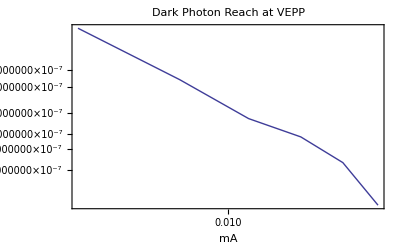

```mathematica
plotVEPP=ListLogLogPlot[ReachTableVEPP, Joined->True, Frame->True, PlotLabel->"Dark Photon Reach at VEPP", FrameLabel->{mA,eps}]
```

```mathematica
Export["ReachPlotVEPP.pdf", plotVEPP]
```

ReachPlotVEPP.pdf

```mathematica
(* ✓  roughly consistent with Fig. 9 of the VEPP-3 proposal, assuming that an extra factor of ~10 improvement in sensitivity from the positron veto is applied *)
```